-Graphics-
🐺 Investigation of motion of the given system taking variety of initial conditions.
-Graphics-
All vector arrows are pointing for Center of Mass

§  Undamped without Driving Force -

Analysis of Dynamics

(r⃗)_A = L (sin(θ_A)-1) i - L cos(θ_A) j 
(r⃗)_B = L (sin(θ_B)+1) i - L cos(θ_B)j
r⃗    = ((r⃗)_A-(r⃗)_B) = L (2+sin(θ_B)-sin(θ_A))i+L (cos(θ_A)-cos(θ_B))j
r     =  | r⃗ |
                                                                                                           (F⃗)_KA=K(r-2L)r̂=K(1-(2L)/r)r⃗=-(F⃗)_KB

OverVector[R_A]  =  L sin(θ_A) i - L cos(θ_A) j
OverVector[R_B]  =  L sin(θ_B) i - L cos(θ_B) j
OverVector[F_A]  =  OverVector[T_A] + K (1-(2L)/r) r⃗ - mg j
OverVector[F_B]  =  OverVector[T_B] - K (1-(2L)/r) r⃗ - mg j
|OverVector[τ_A] | =  | OverVector[R_A] x OverVector[F_A] |  =  -mg L sin(θ_A) + KL^2 (1-(2L)/r) ( 2 cos(θ_A) + cos(θ_A) sin(θ_B) - cos(θ_B) sin(θ_A) )
		(θ^(..))_A =  -g/Lsin(θ_A) + K/m(1-(2L)/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) )
|OverVector[τ_B] | =  | OverVector[R_B] x OverVector[F_B] |  =  -mg L sin(θ_B) + KL^2 (1-(2L)/r) ( 2 cos(θ_B) + cos(θ_B) sin(θ_A) - cos(θ_A) sin(θ_B) )
		(θ^(..))_B  =  -g/Lsin(θ_B) + K/m(1-(2L)/r) ( -2 cos(θ_B) + sin(θ_A-θ_B) )

Non-Dimensionalization

t → √(L/g) t   ,   r → Lr

(θ^(..))_A  =  -sin(θ_A) + K L/mg(1-2/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) )

(θ^(..))_B  =  -sin(θ_B) + K L/mg(1-2/r) ( -2 cos(θ_B) + sin(θ_A-θ_B) )

Module for above Dynamic

```mathematica
Clear[ini,tf,k,c,nMax];
dynamics1[F_,x0_,tf_,k_,nMax_]:=Module[{h,datalist,prev,r1,r2,r3,r4,next},
Clear[h,datalist,prev,r1,r2,r3,r4,next];
h=(tf-x0[[1]])/nMax//N;
For[datalist={x0},
Length[datalist]≤nMax,
AppendTo[datalist,next],
prev=Last[datalist];
r1=Through[F@@prev];
r2=Through[F@@(prev+h/2 r1)];
r3=Through[F@@(prev+h/2 r2)];
r4=Through[F@@(prev+h r3)];
next=prev+h/6(r1+2r2+2r3+r4);
];
Return[datalist];
];

comX1[data_] := Module[{comx},
Clear[comx];
comx=Table[{data[[n,1]],(Sin[data[[n,2]]]+Sin[data[[n,3]]])/2},{n,1,Length[data]}]; 
Return[comx];
];
comY1[data_] := Module[{comy},
Clear[comy];
 comy=Table[{data[[n,1]],1/2(-(Cos[data[[n,2]]]+Cos[data[[n,3]]]))},{n,1,Length[data]}];  
Return[comy];
];
```

```mathematica
Clear[c,k];
r[θ1_,θ2_]=√((2+Sin[θ2]-Sin[θ1])^2+(Cos[θ1]-Cos[θ2])^2);     (* Distance between blocks *)
id[t_,θ1_,θ2_,θ1dot_,θ2dot_]=1;
θ1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=θ1dot;
θ2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=θ2dot;
w1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(2Cos[θ1]-Sin[θ1-θ2])-Sin[θ1];
w2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2];
```

Case 1: Same Initial Angular Displacement

If both blocks initially displaced through same angle then both blocks should move identically as simple pendulum independent of spring.
-Graphics-

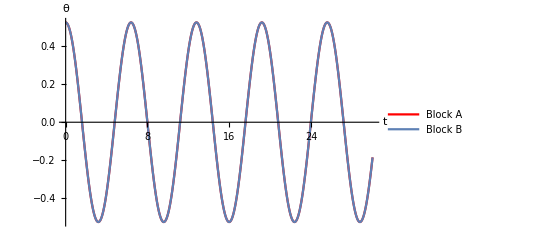
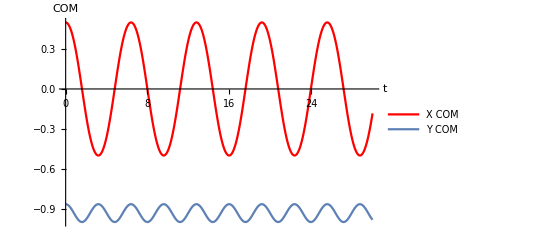

```mathematica
ini={0,π/6,π/6,0,0};       (* Initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=30; 
k= 2;                                                   (* Spring Constant *)
c=1;                                                    (* L/mg *)
nMax=1000;

data=dynamics1[{id,θ1dot,θ2dot,w1dot,w2dot},ini,tf,k,nMax];

comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}]],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

•  From graph it is clear that both blocks have identical angular displacement as both are overlapping.

Now we will confirm independence of spring

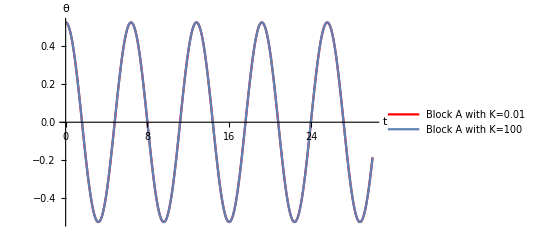

```mathematica
dataK1 = dynamics1[{id, θ1dot, θ2dot, w1dot, w2dot}, ini, tf, 0.01,  nMax];            (* K=0.01 *)
dataK2 = dynamics1[{id, θ1dot, θ2dot, w1dot, w2dot}, ini, tf, 100,  nMax];             (* K=100 *)

 Show[ListPlot[dataK1[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A with K=0.01"}],ListPlot[dataK2[[;;,{1,2}]],Joined->True,PlotLegends->{"Block A with K=100"}]]
```

•  From above graph it is clear motion of blocks is independent of spring as angular displacement of both (k = 0.01 & k = 100) are overlapping.

Case 2: Equal and Opposite Angular Displacement

If both blocks initially displaced through same angle in opposite direction then system would be symmetrical and both blocks will reach their maxima and minima at same time with phase difference of π.

-Graphics-

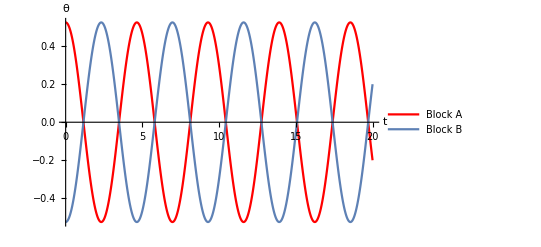
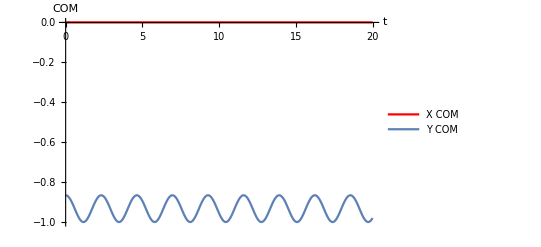

```mathematica
ini={0,π/6,-π/6,0,0};      (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.5;                                              (* spring constant *)
c=1;                                                    (* L/mg *)
nMax=1000;

data=dynamics1[{id,θ1dot,θ2dot,w1dot,w2dot},ini,tf,k,nMax];

comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}]],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

🐺  Observe in this case there is restoring spring force in addition to  gravitational so time period should be lesser than previous case and which is
         clearly justified by both curves. T for previous case (> 6 ) and here (< 5 ).

Case 3: Only one block is initially displaced

In this case Energy & Momentum of displaced block will transfer to other block as a result there will be decrement in amplitude of displaced block 
and simultaneously increment in other block and this pattern will repeat.

-Graphics-

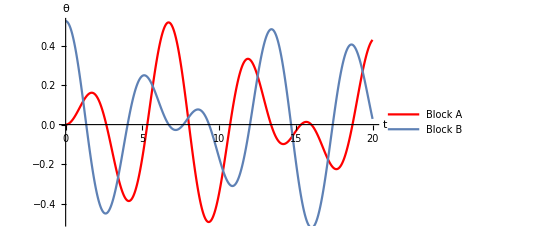
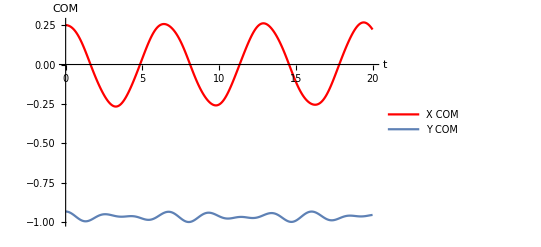

```mathematica
ini={0,0,π/6,0,0};      (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.5;                                       (* spring constant *)
c=1;                                            (* L/mg *)
nMax=1000;

data=dynamics1[{id,θ1dot,θ2dot,w1dot,w2dot},ini,tf,k,nMax];

comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}]],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

•  So, when one block achieves its maxima other achieves its minima.

Case 4: Some initial charges are given

In this case motion will initiate due to interaction between electric fields.
( Here electrodynamics part is neglected )
                                
-Graphics-

OverVector[F_A]  =  OverVector[T_A] + [ K (1-(2L)/r  )-(q_1.q_2)/(4π ϵ r^3)] r⃗ - mg j
OverVector[F_B]  =  OverVector[T_B] + [ -K (1-(2L)/r  )+(q_1.q_2)/(4π ϵ r^3)] r⃗- mg j

|OverVector[τ_A] | =  | OverVector[R_A] x OverVector[F_A] |  =  -mg L sin(θ_A) + [ KL^2 (1-(2L)/r) -(q_1.q_2)/(4π ϵ r^3)L^2] ( 2 cos(θ_A) + cos(θ_A) sin(θ_B) - cos(θ_B) sin(θ_A) )
		(θ^(..))_A  =  -g/L sin(θ_A) + [ K/m(1-(2L)/r) -(q_1.q_2)/(4πϵ m r^3)L^2 ] ( 2 cos(θ_A) - sin(θ_A-θ_B) )
		
|OverVector[τ_B] | =  | OverVector[R_B] x OverVector[F_B] |  =  -mg L sin(θ_B) + [ KL^2 (1-(2L)/r) - (q_1.q_2)/(4π ϵ r^3)L^2 ] ( 2 cos(θ_B) + cos(θ_B) sin(θ_A) - cos(θ_A) sin(θ_B) )
		(θ^(..))_B  =  -g/L sin(θ_B) + [ K/m(1-(2L)/r) - (q_1.q_2)/(4πϵm r^3)L^2 ] ( -2 cos(θ_B) + sin(θ_A-θ_B) )

Non-Dimensionalization

t → √(L/g) t	r → Lr

(θ^(..))_A  =  -sin(θ_A) + [ K L/mg(1-2/r) - 1/(4π ϵ L^3)L/mg(q_1.q_2)/r^3 ] ( 2 cos(θ_A) - sin(θ_A-θ_B) )

(θ^(..))_B  =  -sin(θ_B) + [ K L/mg(1-2/r) - 1/(4π ϵ L^3)L/mg(q_1.q_2)/r^3  ]( -2 cos(θ_B) + sin(θ_A-θ_B) )

```mathematica
Clear[k,c,K,q1,q2];
wq1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=(c k(1-2/r[θ1,θ2])-K c (q1 q2)/(r[θ1,θ2])^3)(2Cos[θ1]-Sin[θ1-θ2])-Sin[θ1];
wq2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=(c k(1-2/r[θ1,θ2])-K c (q1 q2)/(r[θ1,θ2])^3)(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2];
```

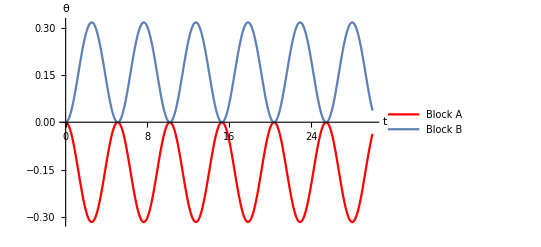
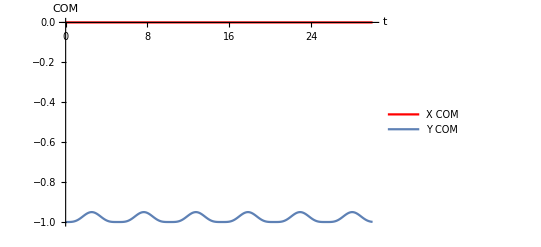

```mathematica
ini={0,0,0,0,0};               (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=30; 
k= 0.1;                                           (* spring constant *)
c=1;                                               (* L/mg *)
K=  10^9;                                            (* K ∝ 1/(4πϵ)1/L^3 *)
q1 = 10^-5;
q2 = 10^-4;
nMax = 1000;                                   
data=dynamics1[{id,θ1dot,θ2dot,wq1dot,wq2dot},ini,tf,k,nMax];

comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

•  (net F_ext=0, x direction) and force on the system is symmetrical in x direction, so there is no displacement of COM in x direction
	Here equilibrium of system will be at (θ_A=-θ & θ_B=+θ)

🐺    To find equilibrium position (±θ) for blocks we have to solve couple of equations by applying condition ( net F_ext=0).
	
But, Observe that, if we start with equilibrium condition then there will be no oscillation.
So, by manipulation of initial parameters we can find equilibrium position (±θ)for the system without dealing with equations.

And we have found out equilibrium position (±θ)to be approx. π/20

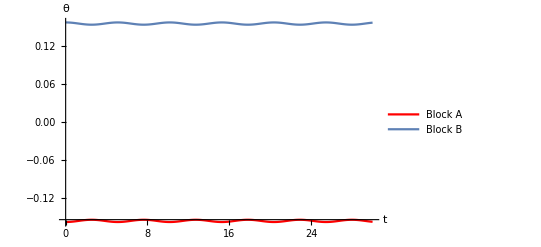

```mathematica
ini = {0,-π/20,π/20,0,0};
data=dynamics1[{id,θ1dot,θ2dot,wq1dot,wq2dot},ini,tf,k,nMax];
Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All]
```

•  It is clear from above plot that equilibrium of system is approx. at θ_A = -π/20 & θ_B = π/20.

§  Damped without Driving Force -

Analysis of Dynamics

OverVector[F_A]  =  OverVector[T_A] + K (1-(2L)/r  ) r⃗ - mg j - b OverVector[V_A]
OverVector[F_B]  =  OverVector[T_B] - K (1-(2L)/r  ) r⃗- mg j - b OverVector[V_B]

|OverVector[τ_A] | =  | OverVector[R_A] x OverVector[F_A] |  =  -mg L sin(θ_A) + KL^2 (1-(2L)/r) ( 2 cos(θ_A) + cos(θ_A) sin(θ_B) - cos(θ_B) sin(θ_A) ) - b LV_B^
		(θ^(..))_A  =  -g/L sin(θ_A) + K/m(1-(2L)/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) ) - (b V_A^)/(m L)
		
|OverVector[τ_B] | =  | OverVector[R_B] x OverVector[F_B] |  =  -mg L sin(θ_B) + [ KL^2 (1-(2L)/r) - b(|OverVector[V_B]|)/r Sign(V_B_x)L^2 ] ( 2 cos(θ_B) + cos(θ_B) sin(θ_A) - cos(θ_A) sin(θ_B) )
		(θ^(..))_B  =  -g/L sin(θ_B) + K/m(1-(2L)/r) ( -2 cos(θ_B) + sin(θ_A-θ_B) ) - (b V_B^)/(m L)

Non-Dimensionalization

t → √(L/g) t   ,   r → Lr   ,   V_A → √(g L)V_A   ,   V_B → √(g L)V_B   

(θ^(..))_A  =  -sin(θ_A) + K L/mg(1-2/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) ) - b/m √(L/g)V_A

(θ^(..))_B  =  -sin(θ_B) + [ K L/mg(1-2/r)( -2 cos(θ_B) + sin(θ_A-θ_B) ) - b/m √(L/g)V_A

Case 5: Damping due to Water drag.

In this case amplitude of blocks will decay due to Water drag opposite to velocity of blocks.
(F⃗)_drag = -6π η R v⃗
(Neglecting Buoyancy)

-Graphics-

```mathematica
Clear[c,k,b];
wd1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(2Cos[θ1]-Sin[θ1-θ2])-Sin[θ1]-b θ1dot[t,θ1,θ2,θ1dot,θ2dot] ;
wd2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2] - b θ2dot[t,θ1,θ2,θ1dot,θ2dot];
```

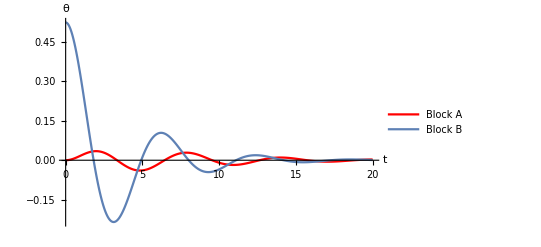
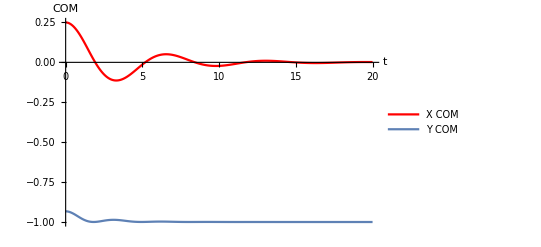

```mathematica
ini={0,0,π/6,0,0};               (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.1;                                                (* spring constant *)
c=1;                                                    (* L/mg *)
b=0.5;                                                (* b ∝ 6πηR *)
nMax = 1000;        

data=dynamics1[{id,θ1dot,θ2dot,wd1dot,wd2dot},ini,tf,k,nMax];
                             
comx=comX1[data];  comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"},PlotRange->All],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"},PlotRange->All],PlotRange->All]]
```

•  Critical damping provides the fastest approach to zero amplitude for in  damped oscillation (Critical damping constant is approx.  b=2)
	On further increasing b it becomes overdamped, which is slowest approach to zero.

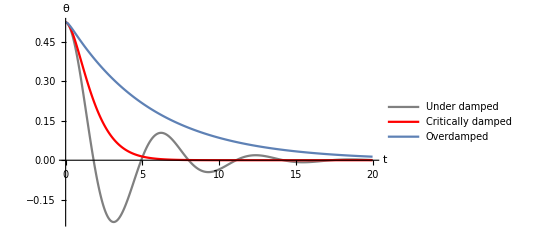

```mathematica
b=2;                                 
data1=dynamics1[{id,θ1dot,θ2dot,wd1dot,wd2dot},ini,tf,k,nMax];

b=6;                                       
 data2=dynamics1[{id,θ1dot,θ2dot,wd1dot,wd2dot},ini,tf,k,nMax];

Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->{Thick,Gray},AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Under damped"},PlotRange->All],ListPlot[data1[[;;,{1,3}]],Joined->True,PlotStyle->{Thick,Red},AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Critically damped"},PlotRange->All],ListPlot[data2[[;;,{1,3}]],Joined->True,PlotLegends->{"Overdamped"},PlotStyle->Thick,PlotRange->All],PlotRange->All]
```

Case 6: Damping due to Eddy currents.

When a conductive material is subjected to a time-varying magnetic flux, eddy currents are generated in the conductor. These eddy currents circulate inside the conductor generating a magnetic field of opposite polarity as the applied magnetic field. The interaction of the two magnetic fields causes a force that resists the change in magnetic flux. However, due to the internal resistance of the conductive material, the eddy currents will be dissipated into heat and the motion will die out.  As the eddy currents are dissipated,energy is removed from the system,thus producing a damping effect.

-Graphics-

```mathematica
ini={0,0,π/6,0,0};               (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.1;                                            (* spring constant *)
c=1;                                                (* L/mg *)
b=0.5;                                          (* b ∝ coefficient of damping (resistance of material) *)
nMax = 1000;        
                             
data=dynamics1[{id,θ1dot,θ2dot,wd1dot,wd2dot},ini,tf,k,nMax];
 
comx=comX1[data];  comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"},PlotRange->All],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"},PlotRange->All],PlotRange->All]]
```

{-Graphics-,-Graphics-}

Case 7: Radiation Damping due to accelerating charge

In radiation damping,  energy of accelerating charges such as electrons is converted to ElectroMagnetic energy .
damping term is given by Larmor radiation rate ∝ γ (q^2 a^2)
 F_damping = (γ a^2)/v , where γ ∝ charge^2
 
 Click here  →  * reference at end of notebook

-Graphics-

```mathematica
clear[c,k,K,γ,q1,q2];

ini={0,0,0,0.01,-0.01};               (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.1;                                                         (* spring constant *)
c=1;                                                              (* L/mg *)
γ=200;                                                       (* b ∝ damping coefficient *)
q1=10^-5;
q2=10^-4;
K=10^9;
nMax = 1000; 

acc={{w1dot@@ini,w2dot@@ini}};
wr1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=(c k(1-2/r[θ1,θ2])-K c (q1 q2)/(r[θ1,θ2])^3-γ *((θ1dot[t,θ1,θ2,θ1dot,θ2dot])^3+(Last[acc][[1]])^2/θ1dot[t,θ1,θ2,θ1dot,θ2dot])/r[θ1,θ2])(2Cos[θ1]-Sin[θ1-θ2])-Sin[θ1];
wr2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=(c k(1-2/r[θ1,θ2])-K c (q1 q2)/(r[θ1,θ2])^3+γ *((θ2dot[t,θ1,θ2,θ1dot,θ2dot])^3+(Last[acc][[2]])^2/θ2dot[t,θ1,θ2,θ1dot,θ2dot])/r[θ1,θ2])(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2];
```

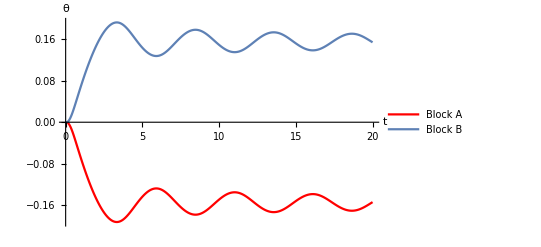
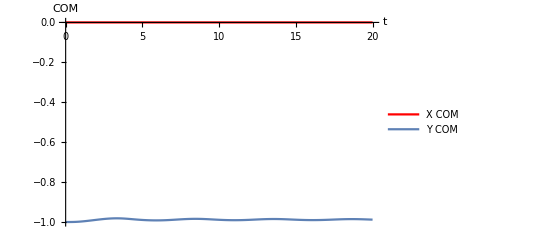

```mathematica
F={id,θ1dot,θ2dot,wr1dot,wr2dot};
For[data={ini};h=tf/nMax,
Length[data]≤nMax,
AppendTo[data,next];AppendTo[acc,nextacc],
prev=Last[data];
r1=Through[F@@prev];
r2=Through[F@@(prev+h/2 r1)];
r3=Through[F@@(prev+h/2 r2)];
r4=Through[F@@(prev+h r3)];
next=prev+h/6(r1+2r2+2r3+r4);
nextacc=Through[{wr1dot,wr2dot}@@prev];
];

comx=comX1[data];  comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"},PlotRange->All],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"},PlotRange->All],PlotRange->All]]
```

§  Undamped with Driving Force -

Analysis of Dynamics

OverVector[F_A]  =  OverVector[T_A] + K (1-(2L)/r) r⃗ - mg j
OverVector[F_B]  =  OverVector[T_B] - K (1-(2L)/r) r⃗ - mg j + F( t )î 

|OverVector[τ_A |]  =  | OverVector[R_A] x OverVector[F_A] |  =  -mg L sin(θ_A) + KL^2 (1-(2L)/r) ( 2 cos(θ_A) + cos(θ_A) sin(θ_B) - cos(θ_B) sin(θ_A) )
		(θ^(..))_A  =  -g/Lsin(θ_A) + K/m(1-(2L)/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) )
		
|OverVector[τ_B |]  =  | OverVector[R_B] x OverVector[F_B] |  =  -mg L sin(θ_B) + F( t ) L cos θ_B + KL^2 (1-(2L)/r) ( 2 cos(θ_B) + cos(θ_B) sin(θ_A) - cos(θ_A) sin(θ_B) )
		(θ^(..))_B  =  -g/Lsin(θ_B) +   (F( t ) cos θ_B )/(m L)+ K/m(1-(2L)/r) ( -2 cos(θ_B) + sin(θ_A-θ_B) )

Non-Dimensionalization

t → √(L/g) t	r → Lr 	  F( t ) ➝ mg F( t ) 

(θ^(..))_A  =  -sin(θ_A) + K L/mg(1-2/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) )

(θ^(..))_B  =  -sin(θ_B) +F( t ) cosθ_B + K L/mg(1-2/r) ( -2 cos(θ_B) + sin(θ_A-θ_B) )

Case 8: Sinusoidal Driving Force



-Graphics-

```mathematica
Clear[c,k,ω]; 
Fex[t_] =0.05* Cos[ω t];
wf1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(2Cos[θ1]-Sin[θ1-θ2])-Sin[θ1];
wf2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2]+ Fex[t]Cos[θ2];
```

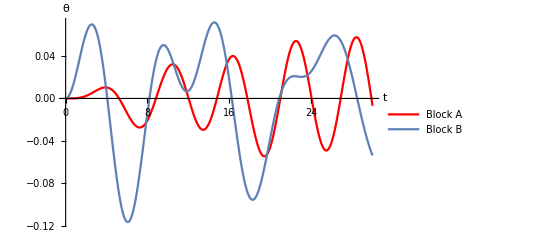
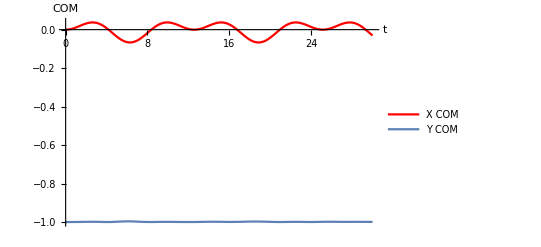

```mathematica
ini={0,0,0,0,0};               (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=30; 
k= 0.1;                                            (* spring constant *)
c=1;                                                (* L/mg *)
ω=0.5;                                            (* Driving Force frequency *)    

nMax = 1000; 

data=dynamics1[{id,θ1dot,θ2dot,wf1dot,wf2dot},ini,tf,k,nMax];

 comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

🐺  Observe that if we increase spring constant then Block A will able to follow Block B.

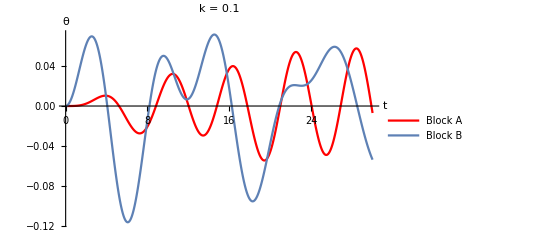
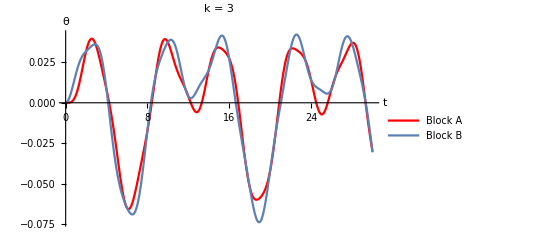

```mathematica
k=3;
datak2=dynamics1[{id,θ1dot,θ2dot,wf1dot,wf2dot},ini,tf,k,nMax];

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All,PlotLabel->Style["k = 0.1",20]],Show[ListPlot[datak2[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[datak2[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All,PlotLabel->Style["k = 3",20]]]
```

•  From above graph clearly our observation is justified.

🐺 Observe if we increase frequency of external force then it will be difficult for Block B to follow its amplitude.

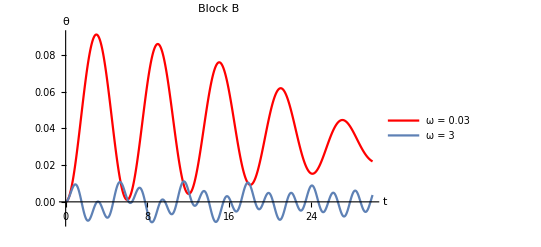

```mathematica
k=0.1;
ω=0.03;
dataw1=dynamics1[{id,θ1dot,θ2dot,wf1dot,wf2dot},ini,tf,k,nMax];

ω=3;
dataw2=dynamics1[{id,θ1dot,θ2dot,wf1dot,wf2dot},ini,tf,k,nMax];

Show[ListPlot[dataw1[[;;,{1,3}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"ω = 0.03"}],ListPlot[dataw2[[;;,{1,3}]],Joined->True,PlotLegends->{"ω = 3"}],PlotRange->All,PlotLabel->Style["Block B",20]]
```

•  From above graph clearly there is significant difference in amplitude.

🐺  From Free oscillation we observed natural frequency of system was approx (2π)/6 so, if driving force will have near that frequency the system will achieve      
              resonance.

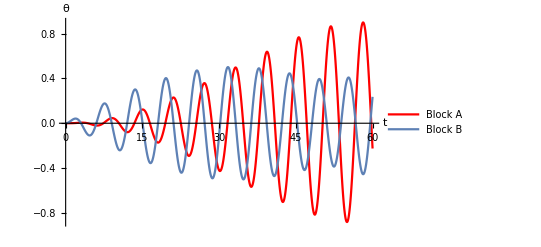

```mathematica
tf=60; 
k= 0.1;   
ω=2π/6;
data=dynamics1[{id,θ1dot,θ2dot,wf1dot,wf2dot},ini,tf,k,nMax];
Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All]
```

🐺   See External force with amplitude just of 0.05 unit make block A to oscillate with such a huge amplitude.
               It’s in RESONANCE !!

Case 9: Impulsive Electric Force

Here Driver  is electric force by impulsive electric field. 

-Graphics-

```mathematica
Clear[c,k,q];
Fex1[t_]=q Sign[Cos[2t]];
wf2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2]+ Fex1[t]Cos[θ2];
```

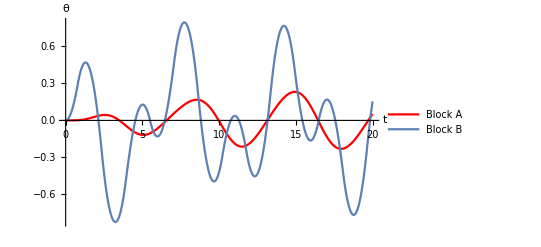
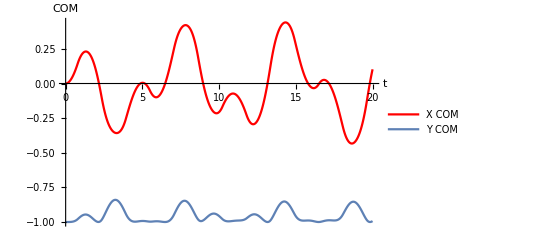

```mathematica
ini={0,0,0,0,0};               (* initial time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.1;                                            (* stiffness for spring *)
c=1;                                               (* L/mg *)
ω=2;  
q=1;                                              

nMax = 1000; 

data=dynamics1[{id,θ1dot,θ2dot,wf1dot,wf2dot},ini,tf,k,nMax];

 comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

Case 10: Constant External Force

Assuming wall is unformally charge and distribution remain unchanged and has very large dimensions as compared to blocks.

-Graphics-
Here  Electric Field is constant(acc to assumption described above) E=σ/2ϵ. where σ is surface charge density.

```mathematica
Clear[c,k,e,q,σ];
Fex2[t_]=e q σ;                   (* e ∝ 1/ϵ *) (* σ is surface charge density *)
wef2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k(1-2/r[θ1,θ2])(-2Cos[θ2]+Sin[θ1-θ2])-Sin[θ2]-e c q σ ;
```

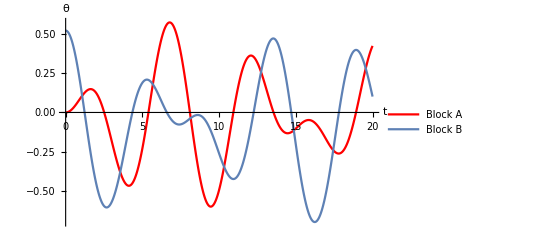
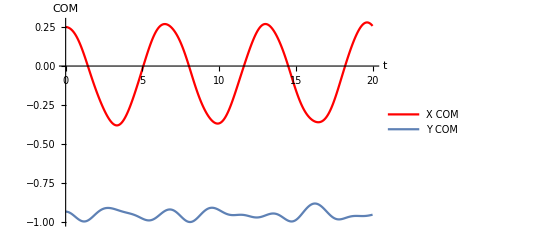

```mathematica
ini={0,0,π/6,0,0};         (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.5;                                          (* spring constant *)
c=1;                                                (* L/mg *)
e=10^9;
q=10^-5;
σ=10^-5;                                                                                            

nMax = 1000; 

data=dynamics1[{id,θ1dot,θ2dot,wf1dot,wef2dot},ini,tf,k,nMax];

 comx=comX1[data]; 
comy=comY1[data]; 

List[Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"}],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"}],PlotRange->All],Show[ListPlot[comx,Joined->True,PlotRange->All,PlotStyle->Red,AxesLabel->{Style[t,15],Style[COM,15]},PlotLegends->{"X COM"}],ListPlot[comy,Joined->True,PlotLegends->{"Y COM"}],PlotRange->All]]
```

§  Damped with Driving Force -

Analysis of Dynamics

OverVector[F_A]  =  OverVector[T_A] + K (1-(2L)/r  ) r⃗ - mg j - b OverVector[V_A] 
OverVector[F_B]  =  OverVector[T_B] - K (1-(2L)/r  ) r⃗- mg j - b OverVector[V_B]  - K'L sin(θ_B) î

|OverVector[τ_A] | =  | OverVector[R_A] x OverVector[F_A] |  =  -mg L sin(θ_A) + KL^2 (1-(2L)/r) ( 2 cos(θ_A) + cos(θ_A) sin(θ_B) - cos(θ_B) sin(θ_A) ) - b LV_B^ 
		(θ^(..))_A  =  -g/L sin(θ_A) + K/m(1-(2L)/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) ) - (b V_A^)/(m L)
		
|OverVector[τ_B] | =  | OverVector[R_B] x OverVector[F_B] |  =  -mg L sin(θ_B) + [ KL^2 (1-(2L)/r) - b(|OverVector[V_B]|)/r Sign(V_B_x)L^2 ] ( 2 cos(θ_B) + cos(θ_B) sin(θ_A) - cos(θ_A) sin(θ_B) )  - K' L^2 sin(θ_B) cos(θ_B) 
		(θ^(..))_B  =  -g/L sin(θ_B) + K/m(1-(2L)/r) ( -2 cos(θ_B) + sin(θ_A-θ_B) ) - (b V_B^)/(m L)  - K'/m sin(θ_B) cos(θ_B)

Non-Dimensionalization

t → √(L/g) t   ,   r → Lr   ,   V_A → √(g L)V_A   ,   V_B → √(g L)V_B   

(θ^(..))_A  =  -sin(θ_A) + K L/mg(1-2/r) ( 2 cos(θ_A) - sin(θ_A-θ_B) ) - b/m √(L/g)V_A 

(θ^(..))_B  =  -sin(θ_B) + [ K L/mg(1-2/r)( -2 cos(θ_B) + sin(θ_A-θ_B) ) - b/m √(L/g)V_A - K' L/mg sin(θ_B) cos(θ_B)

Case 11: External Spring Force

Assuming external spring force always acting horizontally.
( It can by justified by assuming  natural length of external spring >> L )

-Graphics-

```mathematica
Clear[c,k,b,kex];
wfd1dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k (1-2/r[θ1,θ2]) (2 Cos[θ1]-Sin[θ1-θ2])-Sin[θ1]-b*θ1dot[t,θ1,θ2,θ1dot,θ2dot];
wfd2dot[t_,θ1_,θ2_,θ1dot_,θ2dot_]=c k (1-2/r[θ1,θ2]) (-2 Cos[θ2]+Sin[θ1-θ2])-Sin[θ2]-b*θ2dot[t,θ1,θ2,θ1dot,θ2dot]-kex c Sin[θ2]Cos[θ2];
```

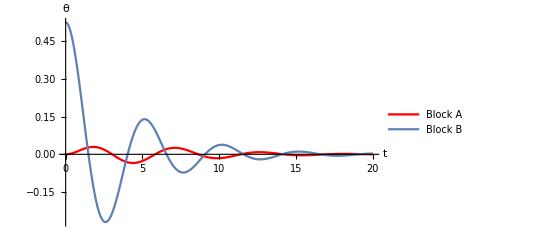

```mathematica
ini={0,0,π/6,0,0};               (* initials: time, θ1, θ2, OverDot[θ1], OverDot[θ2] *)
tf=20; 
k= 0.1;                                              (* spring constant *)
kex=0.5;                                          (* external spring constant *)
c=1;                                                   (* L/mg *)
b=0.5;                                              (* ∝ coefficient of damping *)
nMax = 1000;        
                             
data=dynamics1[{id,θ1dot,θ2dot,wfd1dot,wfd2dot},ini,tf,k,nMax];
 
Show[ListPlot[data[[;;,{1,2}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Block A"},PlotRange->All],ListPlot[data[[;;,{1,3}]],Joined->True,PlotLegends->{"Block B"},PlotRange->All],PlotRange->All]
```

🐺 Observe that for Block B spring are almost in parallel combination so amplitude decay will be at slower rate than in damping without external spring      
          force .

• To confirm this lets plot amplitude curve for block B in both cases

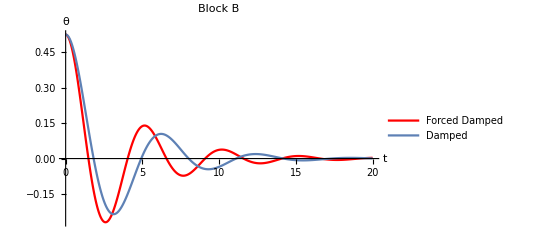

```mathematica
data1=dynamics1[{id,θ1dot,θ2dot,wd1dot,wd2dot},ini,tf,k,nMax];
Show[ListPlot[data[[;;,{1,3}]],Joined->True,PlotStyle->Red,AxesLabel->{Style[t,15],Style[θ,15]},PlotLegends->{"Forced Damped"},PlotRange->All],ListPlot[data1[[;;,{1,3}]],Joined->True,PlotLegends->{"Damped"},PlotRange->All],PlotRange->All,PlotLabel->Style["Block B",20]]
```

• From above graph clearly there is difference in decay rate of amplitude.

References :- 


General Reference
https://www.walter-fendt.de/html5/phen/coupledpendula_en.htm
http://demonstrations.wolfram.com/CoupledPendulumOscillations/

Case: 7
https://www.researchgate.net/publication/270787585_Radiation_Damping_Force_-_An_Alternative_Proposal
http://www.feynmanlectures.caltech.edu/I_32.html